```mathematica
afirst=Import["E:\\Research_Tool\\My_Project\\data_process\\9cell\\9cell1.xlsx"][[1]];
a=Table[afirst[[i]]+{0,5},{i,1,Length[afirst]}];
ax=Table[a[[i,1]],{i,1,Length[a]}];ay=Table[a[[i,2]],{i,1,Length[a]}];
Fay=Fourier[ay];
```

```mathematica
afirst=Import["E:\\Research_Tool\\My_Project\\data_process\\9cell\\test_data.csv"];
a=Table[afirst[[i]]+{0,1000},{i,1,Length[afirst]}];
ax=Table[a[[i,1]],{i,1,Length[a]}];ay=Table[a[[i,2]],{i,1,Length[a]}];
Fay=Fourier[ay];
```

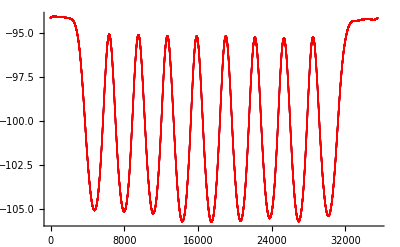

```mathematica
PFay=Table[If[Abs[Fay[[i]]]<1,0,Fay[[i]]],{i,1,Length[a]}];ListPlot[Abs[PFay]];ListFlatteny=Abs[InverseFourier[PFay]];ListFlatten=Table[{ax[[i]],ListFlatteny[[i]]-1000},{i,1,Length[a]}];Show[ListPlot[ListFlatten],ListPlot[afirst,PlotStyle->Red],ImageSize->Full]
```

```mathematica
Export["E:\\Research_Tool\\My_Project\\data_process\\9cell\\9cell1_Fourier_filter_data.csv",ListFlatten]
```

E:\Research_Tool\My_Project\data_process\9cell\9cell1_Fourier_filter_data_test.csv

```mathematica
listvalley=Table[If[ListFlatten[[i,2]]>0,j=0,j=ListFlatten[[i,2]]];{ListFlatten[[i,1]],j},{i,1,Length[ListFlatten]}];listvalley2={};
```

```mathematica
For[i=1,i≤Length[ListFlatten],i++,If[(ListFlatten[[i,2]]-ListFlatten[[i+1,2]])*(ListFlatten[[i+1,2]]-ListFlatten[[i+2,2]])<0,Print[{ListFlatten[[i+1,1]],ListFlatten[[i+1,2]]}]]];
```

{39.,7.79993}

{525.,7.69905}

{768.,7.71147}

{1250.,7.65515}

{1565.,7.66955}

{1916.,7.65848}

{1950.,7.6585}

{4704.,-4.2704}

{6318.,7.32033}

{7886.,-4.10201}

{9476.,7.32196}

{11056.,-4.02256}

{12618.,7.23909}

{14197.,-4.30745}

{15785.,7.30191}

{17380.,-4.07691}

{18949.,7.26939}

{20525.,-3.89854}

{22094.,7.20995}

{23672.,-3.82891}

{25247.,7.26593}

{26834.,-3.82269}

{28405.,7.26894}

{30030.,-3.34725}

{33263.,7.71705}

{34153.,7.65523}

{34647.,7.75511}

{35062.,7.66404}

Part::partw: {{0.,7.79749},{0.,7.79753},{0.,7.79758},{0.,7.79762},{0.,7.79766},{1.,7.7977},{1.,7.79775},{2.,7.79779},{2.,7.79783},{2.,7.79787},«91569»} 的部分 91580 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
width=1000
```

1000

```mathematica
listvalley2=Table[listvalley[[1+i*width;;width+i*width]],{i,0,Length[listvalley]/1000-1}]
```

{{{4000,-0.336613},{4001,-0.345734},{4002,-0.360919},{4003,-0.37002},{4004,-0.376076},{4005,-0.383644},{4006,-0.391205},{4007,-0.397252},{4008,-0.406305},983,{4992,-2.70109},{4993,-2.69896},{4994,-2.69623},{4995,-2.69233},{4996,-2.68973},{4997,-2.68712},{4998,-2.68319},{4999,-2.67662}},25,{1}}
 |  |  |  |

```mathematica
listvalley3=Sort[Table[Sort[listvalley2[[i]],#1[[2]]<#2[[2]]&][[1]],{i,1,Length[listvalley]/1000}],#1[[2]]<#2[[2]]&]
```

{{14237,-3.42789},{4681,-3.254},{20555,-3.20236},{7897,-3.10185},{17417,-3.08538},{8000,-3.04362},{13999,-3.04129},{11049,-2.84546},{26871,-2.84181},{10999,-2.8299},{27000,-2.72539},{5000,-2.67266},{23735,-2.57234},{30081,-2.5299},{29999,-2.49217},{24000,-2.13449},{16999,-1.94218},{21000,-1.76611},{19999,-0.930579},{18000,-0.631091},{15000,0.637127},{22999,0.696167},{25999,2.28078},{12000,2.49541},{6999,2.76544},{28998,4.22829},{9000,4.42641}}

```mathematica
listvalley4={{14237,-3.4278920235959354},{4681,-3.253997541035841},{20555,-3.202357776449174},{7897,-3.1018472786100384},{17417,-3.085382029029094},{8000,-3.0436194337848685},{13999,-3.041291738514238},{11049,-2.845461606512293},{26871,-2.841807594772721},{10999,-2.829898790475027},{27000,-2.7253937885145456},{5000,-2.6726575923318903},{23735,-2.5723449371276215},{30081,-2.5298994591381367},{29999,-2.4921672827350174},{24000,-2.1344896949958105},{16999,-1.942183406522854},{21000,-1.7661122346002942}}
```

{{14237,-3.42789},{4681,-3.254},{20555,-3.20236},{7897,-3.10185},{17417,-3.08538},{8000,-3.04362},{13999,-3.04129},{11049,-2.84546},{26871,-2.84181},{10999,-2.8299},{27000,-2.72539},{5000,-2.67266},{23735,-2.57234},{30081,-2.5299},{29999,-2.49217},{24000,-2.13449},{16999,-1.94218},{21000,-1.76611}}

```mathematica
listvalley5=Sort[listvalley4]
```

{{4681,-3.254},{5000,-2.67266},{7897,-3.10185},{8000,-3.04362},{10999,-2.8299},{11049,-2.84546},{13999,-3.04129},{14237,-3.42789},{16999,-1.94218},{17417,-3.08538},{20555,-3.20236},{21000,-1.76611},{23735,-2.57234},{24000,-2.13449},{26871,-2.84181},{27000,-2.72539},{29999,-2.49217},{30081,-2.5299}}

```mathematica
listvalley6={{4681,-3.253997541035841},{7897,-3.1018472786100384},{11049,-2.845461606512293},{14237,-3.4278920235959354},{17417,-3.085382029029094},{20555,-3.202357776449174},{23735,-2.5723449371276215},{26871,-2.841807594772721},{30081,-2.5298994591381367}}
```

{{4681,-3.254},{7897,-3.10185},{11049,-2.84546},{14237,-3.42789},{17417,-3.08538},{20555,-3.20236},{23735,-2.57234},{26871,-2.84181},{30081,-2.5299}}

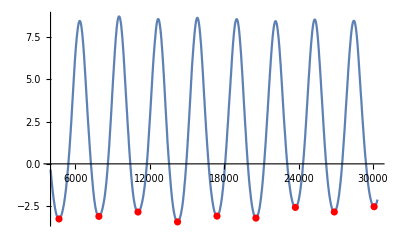

```mathematica
Show[Plot[ifun[x],{x,4000,30350}],ListPlot[listvalley6,PlotStyle->Red]]
```